# Everything is an expression.

算术表达式

```mathematica
2a+√b+c^d[e]//FullForm
```

Plus[Times[2,a],Power[b,Rational[1,2]],Power[c,d[e]]]

列表

```mathematica
{1+2I,a*b+c,{2,a},"Str"}//FullForm
```

List[Complex[1,2],Plus[Times[a,b],c],List[2,a],"Str"]

图形

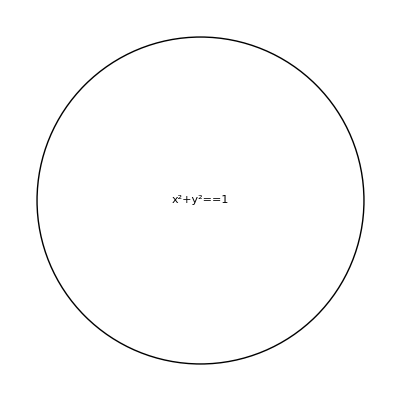
```mathematica
-Graphics-//FullForm
```

Graphics[List[Circle[List[0,0]],Inset[Equal[Plus[Power[x,2],Power[y,2]],1],List[0,0]]]]

非符号头部的表达式

```mathematica
(1+#)&[a]//Hold//FullForm
```

Hold[Function[Plus[1,Slot[1]]][a]]

按钮控件

```mathematica
"Push"//FullForm
```

Button["Push",Print["Push!"],Rule[Appearance,Automatic],Rule[Evaluator,Automatic],Rule[Method,"Preemptive"]]

笔记本

```mathematica
CreateDocument[{x+y,1/x+1/y}]//NotebookGet//FullForm
```

Notebook[List[Cell[BoxData[RowBox[List["x","+","y"]]]],Cell[BoxData[RowBox[List[FractionBox["1","x"],"+",FractionBox["1","y"]]]]]],Rule[WindowSize,List[582.6,493.2]],Rule[WindowMargins,List[List[279,Automatic],List[Automatic,40.2]]],Rule[FrontEndVersion,"12.1 for Microsoft Windows (64-bit) (2020\:5e744\:670815\:65e5)"],Rule[StyleDefinitions,"Default.nb"]]